## Usage

## Initialize

```mathematica
$HistoryLength=1;
ClearAll["Global`*"];
Off[General::spell, General::spell1]
```

```mathematica
Needs["ErrorBarPlots`"]
```

## Generate global Har translation decay plots

### Reading In Parameters:

```mathematica
AALength=1428;
myStartTime=5;
myEndTime=65;
```

```mathematica
sampleSize = Length@onlyYellowSpots  ;
(* sampleSize usually uses the same # as sample size, in my case, number of cells*) 
repetitions = 30  ;(* this is repetition of finding the mean of BS data needs to be at least 20 or 30*)
```

### Reading In Files

```mathematica
analysisFolder = "/Volumes/MINI/_har TEMP use for global analysis/"
```

/Volumes/MINI/_har TEMP use for global analysis/

```mathematica
myFolders = {"/Volumes/MINI/_har TEMP use for global analysis/20180910_Har/Analysis",     "/Volumes/MINI/_har TEMP use for global analysis/20180926_harringtonine_TL_TA/Analysis",  "/Volumes/MINI/_har TEMP use for global analysis/20181024_har_TA/Analysis",  "/Volumes/MINI/_har TEMP use for global analysis/20181026_TLhar/Analysis",  "/Volumes/MINI/_har TEMP use for global analysis/20181027_TL_same cells as overnight_HAR/Analysis" };
```

```mathematica
myYellowOnlyFiles = Table[FileNames[(myFolders[[i]]<>"/*_ySpotNTime.m")],{i,1,Length@myFolders,1}];
Length@myYellowOnlyFiles
```

5

```mathematica
myWhiteFiles = Table[FileNames[(myFolders[[i]]<>"/*_wSpotNTime.m")],{i,1,Length@myFolders,1}];
Length@myWhiteFiles
```

5

```mathematica
myAllYellowFiles = Table[FileNames[(myFolders[[i]]<>"/*_gSpotNTime.m")],{i,1,Length@myFolders,1}];
Length@myAllYellowFiles
```

5

```mathematica
myPurpleFiles = Table[FileNames[(myFolders[[i]]<>"/*_brSpotNTime.m")],{i,1,Length@myFolders,1}];
Length@myPurpleFiles
```

5

### Yellow Only Har translation decay

```mathematica
onlyYellow = Table[Table[Import[myYellowOnlyFiles⟦i,j⟧],{j,1,Length@myYellowOnlyFiles⟦i⟧,1}],{i,1,Length@myYellowOnlyFiles,1}]//#[[2;;3]]&//Flatten[#,1]& ;
```

```mathematica
cellCount = Length@onlyYellow
```

6

```mathematica
spotCount = Total[Transpose[onlyYellow],{2}]//#[[All,2]]&;
times = Total[Transpose[onlyYellow],{2}]//#[[All,1]]/cellCount&;
```

```mathematica
yelOnlySpotCount= Transpose[{times,spotCount}](*Combining Time with the # of spots*)
```

{{-178,65},{-118,61},{-58,57},{2,62},{62,55},{122,51},{182,49},{242,59},{302,59},{362,48},{422,41},{482,43},{542,40},{602,35},{662,28},{722,34},{782,33},{842,34},{902,34},{962,26},{1022,28},{1082,26},{1142,33},{1202,19},{1262,29},{1322,27},{1382,27},{1442,29},{1502,28},{1562,25},{1622,20},{1682,21},{1742,26},{1802,25},{1862,17},{1922,18},{1982,27},{2042,21},{2102,19},{2162,14},{2222,25},{2282,19},{2342,16},{2402,17},{2462,13},{2522,20},{2582,14},{2642,12},{2702,15},{2762,13},{2822,13},{2882,18},{2942,13},{3002,15},{3062,17},{3122,10},{3182,11},{3242,13},{3302,13},{3362,13},{3422,10},{3482,6},{3542,10},{3602,17},{3662,8}}

{{-178,65},{-118,61},{-58,57},{2,62},{62,55},{122,51},{182,49},{242,59},{302,59},{362,48},{422,41},{482,43},{542,40},{602,35},{662,28},{722,34},{782,33},{842,34},{902,34},{962,26},{1022,28},{1082,26},{1142,33},{1202,19},{1262,29},{1322,27},{1382,27},{1442,29},{1502,28},{1562,25},{1622,20},{1682,21},{1742,26},{1802,25},{1862,17},{1922,18},{1982,27},{2042,21},{2102,19},{2162,14},{2222,25},{2282,19},{2342,16},{2402,17},{2462,13},{2522,20},{2582,14},{2642,12},{2702,15},{2762,13},{2822,13},{2882,18},{2942,13},{3002,15},{3062,17},{3122,10},{3182,11},{3242,13},{3302,13},{3362,13},{3422,10},{3482,6},{3542,10},{3602,17},{3662,8}}

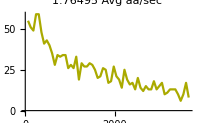
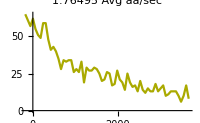
{{1.76495,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = yelOnlySpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{yelOnlyTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
myYelOnlySpotTime = spotTime;
Export[analysisFolder<>"_yOnlyGlobalTimePlot.tif",yelOnlyTimePlot];
spotTime>>analysisFolder<>"_OnlyGlobalTime.m"
```

### Yellow All Har translation decay

```mathematica
allYellow = Table[Table[Import[myAllYellowFiles[[i,j]]],{j,1,Length@myAllYellowFiles[[i]],1}],{i,1,Length@myAllYellowFiles,1}]//#[[2;;3]]&//Flatten[#,1]&;
```

```mathematica
cellCount = Length@allYellow
```

6

```mathematica
spotCount = Total[Transpose[allYellow],{2}]//#[[All,2]]&;
```

```mathematica
yelAllSpotCount= Transpose[{times,spotCount}](*Combining Time with the # of spots*)
```

{{-178,109},{-118,103},{-58,91},{2,91},{62,92},{122,79},{182,86},{242,87},{302,88},{362,79},{422,69},{482,63},{542,70},{602,67},{662,54},{722,64},{782,65},{842,59},{902,61},{962,51},{1022,49},{1082,51},{1142,53},{1202,44},{1262,55},{1322,53},{1382,55},{1442,48},{1502,50},{1562,50},{1622,40},{1682,42},{1742,47},{1802,42},{1862,33},{1922,40},{1982,42},{2042,37},{2102,33},{2162,29},{2222,39},{2282,34},{2342,29},{2402,27},{2462,30},{2522,32},{2582,30},{2642,29},{2702,27},{2762,26},{2822,20},{2882,29},{2942,22},{3002,26},{3062,25},{3122,13},{3182,18},{3242,19},{3302,21},{3362,16},{3422,13},{3482,13},{3542,14},{3602,21},{3662,15}}

{{-178,109},{-118,103},{-58,91},{2,91},{62,92},{122,79},{182,86},{242,87},{302,88},{362,79},{422,69},{482,63},{542,70},{602,67},{662,54},{722,64},{782,65},{842,59},{902,61},{962,51},{1022,49},{1082,51},{1142,53},{1202,44},{1262,55},{1322,53},{1382,55},{1442,48},{1502,50},{1562,50},{1622,40},{1682,42},{1742,47},{1802,42},{1862,33},{1922,40},{1982,42},{2042,37},{2102,33},{2162,29},{2222,39},{2282,34},{2342,29},{2402,27},{2462,30},{2522,32},{2582,30},{2642,29},{2702,27},{2762,26},{2822,20},{2882,29},{2942,22},{3002,26},{3062,25},{3122,13},{3182,18},{3242,19},{3302,21},{3362,16},{3422,13},{3482,13},{3542,14},{3602,21},{3662,15}}

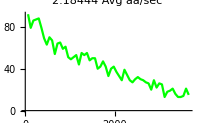
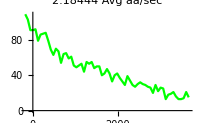
{{2.18444,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = yelAllSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{yelAllTimePlot=spotTime//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
yelAllTime = spotTime;
Export[analysisFolder<>"_yAllGlobalTimePlot.tif",yelAllTimePlot];
yelAllTimePlot>>analysisFolder<>"_yAllGlobalTime.m"
```

### White Har translation decay

```mathematica
white = Table[Table[Import[myWhiteFiles[[i,j]]],{j,1,Length@myWhiteFiles[[i]],1}],{i,1,Length@myWhiteFiles,1}]//#[[2;;3]]&//Flatten[#,1]&;
```

```mathematica
cellCount = Length@white
```

6

```mathematica
spotCount = Total[Transpose[white],{2}]//#[[All,2]]&;
times = Total[Transpose[white],{2}]//#[[All,1]]/cellCount&;
```

```mathematica
whiteSpotCount= Transpose[{times,spotCount}](*Combining Time with the # of spots*)
```

{{-178,44},{-118,42},{-58,34},{2,29},{62,37},{122,28},{182,37},{242,28},{302,29},{362,31},{422,28},{482,20},{542,30},{602,32},{662,26},{722,30},{782,32},{842,25},{902,27},{962,25},{1022,21},{1082,25},{1142,20},{1202,25},{1262,26},{1322,26},{1382,28},{1442,19},{1502,22},{1562,25},{1622,20},{1682,21},{1742,21},{1802,17},{1862,16},{1922,22},{1982,15},{2042,16},{2102,14},{2162,15},{2222,14},{2282,15},{2342,13},{2402,10},{2462,17},{2522,12},{2582,16},{2642,17},{2702,12},{2762,13},{2822,7},{2882,11},{2942,9},{3002,11},{3062,8},{3122,3},{3182,7},{3242,6},{3302,8},{3362,3},{3422,3},{3482,7},{3542,4},{3602,4},{3662,7}}

{{-178,44},{-118,42},{-58,34},{2,29},{62,37},{122,28},{182,37},{242,28},{302,29},{362,31},{422,28},{482,20},{542,30},{602,32},{662,26},{722,30},{782,32},{842,25},{902,27},{962,25},{1022,21},{1082,25},{1142,20},{1202,25},{1262,26},{1322,26},{1382,28},{1442,19},{1502,22},{1562,25},{1622,20},{1682,21},{1742,21},{1802,17},{1862,16},{1922,22},{1982,15},{2042,16},{2102,14},{2162,15},{2222,14},{2282,15},{2342,13},{2402,10},{2462,17},{2522,12},{2582,16},{2642,17},{2702,12},{2762,13},{2822,7},{2882,11},{2942,9},{3002,11},{3062,8},{3122,3},{3182,7},{3242,6},{3302,8},{3362,3},{3422,3},{3482,7},{3542,4},{3602,4},{3662,7}}

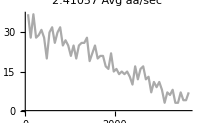
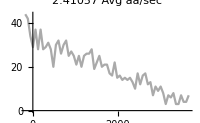
{{2.41057,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = whiteSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{whiteTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_wGlobalTimePlot.tif",whiteTimePlot];
whiteTimePlot>>analysisFolder<>"_wGlobalTime.m"
```

### Purple Har translation decay

```mathematica
purple = Table[Table[Import[myPurpleFiles[[i,j]]],{j,1,Length@myPurpleFiles[[i]],1}],{i,1,Length@myPurpleFiles,1}]//#[[2;;3]]&//Flatten[#,1]&;
```

```mathematica
cellCount = Length@purple
```

6

```mathematica
spotCount = Total[Transpose[purple],{2}]//#[[All,2]]&;
times = Total[Transpose[purple],{2}]//#[[All,1]]/cellCount&;
purpleSpotCount= Transpose[{times,spotCount}](*Combining Time with the # of spots*)
```

{{-178,151},{-118,152},{-58,128},{2,130},{62,142},{122,142},{182,144},{242,150},{302,141},{362,145},{422,134},{482,154},{542,146},{602,145},{662,157},{722,138},{782,155},{842,151},{902,157},{962,149},{1022,136},{1082,146},{1142,138},{1202,149},{1262,149},{1322,151},{1382,153},{1442,145},{1502,168},{1562,154},{1622,155},{1682,139},{1742,144},{1802,134},{1862,137},{1922,131},{1982,141},{2042,148},{2102,150},{2162,149},{2222,134},{2282,160},{2342,150},{2402,154},{2462,144},{2522,158},{2582,149},{2642,157},{2702,148},{2762,142},{2822,149},{2882,145},{2942,143},{3002,164},{3062,146},{3122,148},{3182,151},{3242,132},{3302,136},{3362,138},{3422,157},{3482,153},{3542,144},{3602,141},{3662,152}}

{{-178,151},{-118,152},{-58,128},{2,130},{62,142},{122,142},{182,144},{242,150},{302,141},{362,145},{422,134},{482,154},{542,146},{602,145},{662,157},{722,138},{782,155},{842,151},{902,157},{962,149},{1022,136},{1082,146},{1142,138},{1202,149},{1262,149},{1322,151},{1382,153},{1442,145},{1502,168},{1562,154},{1622,155},{1682,139},{1742,144},{1802,134},{1862,137},{1922,131},{1982,141},{2042,148},{2102,150},{2162,149},{2222,134},{2282,160},{2342,150},{2402,154},{2462,144},{2522,158},{2582,149},{2642,157},{2702,148},{2762,142},{2822,149},{2882,145},{2942,143},{3002,164},{3062,146},{3122,148},{3182,151},{3242,132},{3302,136},{3362,138},{3422,157},{3482,153},{3542,144},{3602,141},{3662,152}}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

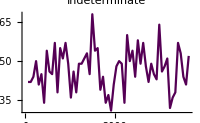
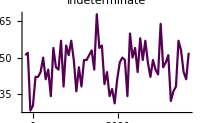
{{Indeterminate,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = purpleSpotCount
purpleSpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{purpleTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_pGlobalTimePlot.tif",purpleTimePlot];
purpleSpotWeights>>analysisFolder<>"_pGlobalTime.m"
```

### View it all...

```mathematica
Row[{purpleTimePlot,whiteTimePlot,yelOnlyTimePlot,yelAllTimePlot
}]
```

-Graphics--Graphics--Graphics--Graphics-

## Bootstrapping the datasets:

### Reading In BS Parameters:

```mathematica
sampleSize = Length@onlyYellowSpots  
(* sampleSize usually uses the same # as sample size, in my case, number of cells*) 
repetitions = 30  (* this is repetition of finding the mean of BS data needs to be at least 20 or 30*)
```

6

30

### BS for Only Yellow Spots:

```mathematica
onlyYellow//Dimensions
```

{6,65,2}

```mathematica
onlyYellowSpots = onlyYellow[[All,All,2]];
onlyYellowSpots
```

{{6,8,7,6,5,7,5,8,11,7,4,3,4,6,5,4,5,5,5,5,4,5,3,5,2,4,5,5,5,5,4,2,3,6,3,1,6,3,7,1,7,5,4,2,2,4,3,1,4,3,2,6,4,4,1,4,1,4,5,5,2,2,2,3,1},{14,15,12,15,15,7,10,12,6,12,12,14,11,10,6,12,11,10,8,7,9,9,11,3,8,8,4,3,9,7,7,5,9,10,7,5,8,2,4,4,4,4,6,3,4,4,4,3,5,1,4,3,3,5,7,1,2,3,4,2,1,0,1,4,2},{3,1,2,1,5,4,1,2,5,2,2,5,2,2,1,3,1,2,1,1,1,0,2,4,7,1,1,2,3,1,0,1,3,1,0,1,3,0,0,1,1,2,2,2,1,2,1,2,0,1,1,3,0,0,1,0,1,1,1,0,1,0,0,4,0},{7,5,10,10,9,7,7,6,8,8,7,6,6,6,5,4,4,5,5,3,5,4,4,2,1,3,4,5,2,2,3,3,3,0,2,3,3,3,2,1,3,2,1,1,1,2,1,1,2,1,1,1,1,1,2,2,2,2,2,1,2,2,2,0,1},{26,25,19,20,14,19,21,16,22,13,9,8,10,9,5,7,7,8,8,7,6,6,8,4,8,6,7,9,5,7,3,5,6,6,4,4,5,7,4,5,6,2,2,5,2,8,2,5,2,5,2,4,4,5,4,3,4,2,1,4,3,2,3,3,3},{9,7,7,10,7,7,5,15,7,6,7,7,7,2,6,4,5,4,7,3,3,2,5,1,3,5,6,5,4,3,3,5,2,2,1,4,2,6,2,2,4,4,1,4,3,0,3,0,2,2,3,1,1,0,2,0,1,1,0,1,1,0,2,3,1}}

```mathematica
(*
DEV: 
I dont think this is right..need one error of all the means instead of the dev of data from each mean 

stdevsBS = Table[Table[StandardDeviation[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}]//Transpose;
errorBS = Table[ErrorBar/@stdevsBS[[i]],{i,1,Length@stdevsBS,1}];
b = Table[Transpose[{meanTimeBS[[i]],errorBS[[i]]}],{i,1,Length@meansBS,1}];
Dimensions/@b
Dimensions/@meansBS
meanTimeBS = Table[Transpose[{Table[times,Length@meansBS][[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];

*)
```

```mathematica
a = Table[Table[Table[RandomChoice[onlyYellowSpots[[All,i]]],sampleSize],repetitions ],{i,1,Length@yelOnlySpotCount,1}];
```

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
stdevsBS = N/@StandardDeviation/@meansBS 
errorBS =ErrorBar/@stdevsBS;
Length@meansBS
Length@stdevsBS
```

{3.3142,3.84511,1.99217,2.74688,1.33506,1.88071,2.73888,2.0126,3.34089,1.73279,1.251,1.33687,1.22234,1.12712,0.607031,1.09377,1.13546,0.98449,0.901344,1.05021,0.924427,1.00928,1.10093,0.496604,1.56163,0.946004,0.927376,0.667648,1.08055,1.01307,0.944315,0.648237,1.12012,1.21921,0.778892,0.598022,0.707761,1.0274,1.01441,0.580549,0.726725,0.423187,0.692507,0.636883,0.46255,1.08254,0.412759,0.697125,0.568545,0.583429,0.458912,0.641677,0.561539,1.02048,0.728042,0.612763,0.410588,0.470354,0.616426,0.75186,0.365367,0.437104,0.410432,0.616426,0.351107}

65

65

```mathematica
meansBS[[1]]
Length/@meansBS
```

{12.6667,9.33333,8.16667,10.1667,13.8333,10.1667,14.8333,10.1667,6.66667,11.5,5.83333,12.,13.6667,11.6667,13.6667,14.5,8.16667,12.8333,9.5,9.83333,7.,8.16667,8.,14.3333,18.,17.,12.8333,6.33333,9.5,7.83333}

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
c = Table[times,repetitions]//Transpose;
```

```mathematica
Length@c
Length/@c
```

65

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
repTimes = Table[times,repetitions]//Transpose;
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
```

```mathematica
b = Transpose[{myYelOnlySpotTime ,errorBS}];
```

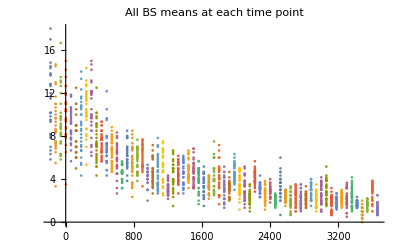

```mathematica
ListPlot[
meanTimeBS,PlotLabel->"All BS means at each time point"]
```

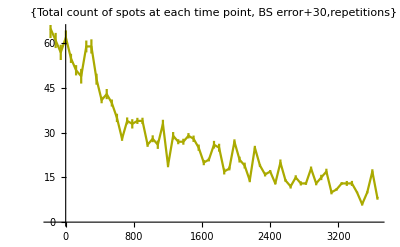

```mathematica
ErrorListPlot[b,PlotStyle->{Darker[Yellow]}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True]
```

### BS for Only Yellow Spots:

ALL OF THIS BS FOR ONLY YELLOW SPOTS SHIT IS BROKE AS FUCK!!!! FIX THIS SHIT

```mathematica
allYellow//Dimensions
Dimensions/@onlyYellowSpots
Dimensions/@allYellowSpots
```

{6,65,2}

{{65},{65},{65},{65},{65},{65}}

{{65},{65},{65},{65},{65},{65}}

```mathematica
allYellowSpots= allYellow[[All,All,2]];
allYellowSpots
```

{{8,10,11,11,9,10,9,10,14,9,7,6,9,8,8,8,6,6,6,8,7,7,4,7,3,6,7,7,7,10,8,7,7,8,7,7,8,9,7,3,8,6,6,4,6,4,4,2,5,4,4,7,6,5,3,4,3,6,6,5,3,4,3,4,4},{25,25,21,25,23,12,21,22,17,25,20,22,23,20,13,24,19,18,20,16,17,22,22,13,19,20,17,14,21,17,18,12,19,17,12,15,13,8,7,11,8,9,12,8,11,12,10,12,12,8,7,5,5,10,9,3,4,4,9,4,1,3,3,7,3},{10,10,5,3,12,9,7,8,7,7,4,6,7,6,4,7,6,8,4,5,4,1,4,7,8,4,3,2,4,2,1,5,3,1,1,1,3,0,0,1,1,2,2,3,2,2,3,4,0,2,1,5,0,2,2,0,2,2,1,1,2,0,0,4,0},{7,5,10,10,9,7,8,6,8,8,7,6,6,6,5,4,4,5,5,3,5,4,4,2,1,3,4,5,2,2,3,3,3,0,2,3,3,3,2,1,3,2,1,1,1,2,1,1,2,1,1,1,1,1,2,2,2,2,2,1,2,2,2,0,1},{33,31,24,22,18,20,26,18,25,16,13,9,11,12,6,9,12,9,9,8,8,8,9,5,13,9,12,9,8,8,4,6,8,7,7,5,8,9,8,7,8,5,3,6,4,10,6,6,2,5,3,5,5,7,4,4,4,3,2,4,3,2,3,3,5},{26,22,20,20,21,21,15,23,17,14,18,14,14,15,18,12,18,13,17,11,8,9,10,10,11,11,12,11,8,11,6,9,7,9,4,9,7,8,9,6,11,10,5,5,6,2,6,4,6,6,4,6,5,1,5,0,3,2,1,1,2,2,3,3,2}}

```mathematica
a = Table[Table[Table[RandomChoice[allYellowSpots[[All,i]]],sampleSize],repetitions ],{i,1,Length@allYellowSpots,1}]
```

{{{26,26,26,8,26,10},{26,8,7,33,26,25},{7,10,7,8,10,8},{26,10,33,10,26,33},{25,33,25,33,8,8},{25,10,10,25,8,33},{7,25,26,33,8,8},{8,33,7,10,26,26},{10,33,7,7,33,10},{7,26,26,7,7,33},{10,33,7,7,10,7},{33,33,10,10,8,8},{7,33,33,7,26,8},{26,26,33,33,25,7},{26,7,7,33,26,25},{26,33,25,25,25,26},{7,7,8,7,7,25},{7,10,25,33,25,7},{25,7,7,8,33,7},{10,8,26,33,33,7},{26,10,25,8,10,8},{26,33,26,33,10,26},{7,25,25,8,7,33},{7,10,26,10,7,8},{7,26,8,26,10,10},{26,8,8,8,10,8},{26,33,33,25,25,10},{8,7,26,33,7,33},{7,8,25,26,8,7},{26,26,7,7,7,10}},{{31,22,31,5,22,10},{22,5,31,10,22,5},{25,10,10,31,25,25},{22,10,5,5,31,31},{10,25,31,5,10,10},{25,10,10,10,25,22},{25,25,25,25,31,22},{31,10,10,22,5,22},{25,31,25,25,10,22},{5,5,31,5,25,5},{5,25,10,5,10,5},{25,31,25,5,10,10},{10,10,10,25,22,25},{10,25,10,25,22,10},{10,22,25,25,10,10},{10,10,5,5,5,10},{31,10,22,5,10,10},{5,31,10,31,5,10},{22,10,10,5,10,25},{25,10,5,25,10,10},{31,25,10,10,5,5},{22,25,10,10,5,22},{25,10,10,5,25,31},{25,25,10,25,5,10},{22,31,22,10,22,10},{31,22,25,5,31,10},{22,25,31,10,22,10},{22,25,10,25,31,31},{5,10,31,22,31,25},{5,31,10,25,10,31}},{{10,20,11,10,20,5},{10,11,20,5,20,5},{11,11,5,20,20,10},{20,5,11,11,21,5},{21,20,10,24,11,24},{5,11,10,10,10,10},{5,5,10,11,11,10},{5,21,20,10,5,5},{11,11,10,10,5,20},{10,21,11,24,5,24},{11,24,5,24,20,11},{10,5,20,24,5,24},{21,24,24,11,24,24},{20,24,20,11,20,10},{21,10,20,5,5,21},{24,20,24,11,10,24},{5,24,10,5,24,5},{5,11,11,21,20,20},{10,5,5,24,5,21},{21,11,10,5,10,11},{10,21,10,10,24,20},{5,24,20,11,20,21},{5,5,5,24,11,24},{11,11,24,21,5,10},{21,24,24,20,5,21},{24,5,24,11,11,24},{21,21,5,10,20,11},{11,24,21,24,5,20},{5,11,11,21,20,24},{10,11,10,11,21,11}},{{10,3,11,22,11,20},{10,20,22,22,25,11},{22,3,10,3,3,10},{11,20,10,3,11,3},{10,3,22,20,11,22},{25,25,22,11,20,10},{22,25,25,3,11,22},{10,20,22,20,25,22},{11,3,20,20,25,22},{3,25,20,3,11,11},{22,20,20,3,3,3},{11,3,10,22,3,25},{22,11,25,25,10,25},{22,20,3,11,11,22},{22,25,11,20,3,22},{3,22,11,10,3,20},{22,22,11,3,3,11},{22,25,10,10,11,10},{25,20,11,10,11,20},{25,25,20,11,10,20},{20,20,22,3,10,25},{22,20,20,22,10,11},{3,22,3,20,11,20},{22,25,22,20,22,10},{20,3,20,25,22,25},{3,11,20,25,20,10},{10,11,11,3,3,20},{20,20,20,22,25,20},{20,11,10,22,11,25},{3,25,3,3,20,25}},{{18,18,23,18,23,21},{12,23,12,12,18,9},{12,23,18,9,18,18},{12,18,12,12,23,23},{23,9,9,21,12,18},{9,9,18,18,23,12},{18,21,9,23,12,12},{18,9,12,21,18,21},{12,23,9,23,23,18},{18,18,21,21,9,9},{23,9,9,21,9,23},{18,9,23,21,12,9},{12,9,9,9,23,9},{12,9,21,18,18,9},{21,9,21,9,9,18},{9,9,23,21,12,12},{9,18,18,9,18,9},{18,9,9,23,23,9},{21,23,9,9,9,9},{9,9,12,21,18,23},{18,12,9,23,9,21},{21,12,23,9,18,23},{12,23,23,18,9,18},{21,9,9,23,12,9},{12,9,18,9,21,12},{12,12,9,9,18,23},{9,12,23,9,21,23},{12,9,9,9,9,18},{12,18,18,12,9,18},{12,9,12,12,21,9}},{{10,20,9,21,7,7},{12,20,7,21,9,12},{21,10,21,9,9,21},{10,21,7,9,9,12},{20,20,7,12,21,12},{10,9,20,10,7,21},{12,9,9,21,20,20},{12,12,7,20,20,21},{7,21,7,21,20,7},{7,12,21,10,21,12},{21,7,7,9,21,9},{21,7,20,9,10,20},{21,9,12,12,20,12},{9,7,21,9,10,7},{12,12,10,12,21,21},{9,7,21,21,12,21},{7,7,20,10,9,10},{12,9,20,7,21,21},{20,10,21,20,10,20},{20,7,12,20,20,9},{20,7,12,21,20,7},{10,12,10,20,9,21},{10,9,7,7,21,10},{9,20,21,12,9,21},{7,12,10,9,7,10},{21,7,21,7,10,21},{9,12,12,20,21,21},{9,10,21,20,10,10},{20,7,10,9,21,7},{10,20,9,10,21,7}}}

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
stdevsBS = N/@StandardDeviation/@meansBS 
errorBS =ErrorBar/@stdevsBS;
Length@meansBS
Length@stdevsBS
```

{3.74055,4.17069,2.57432,3.16734,2.1541,2.34251}

6

6

```mathematica
meansBS[[1]]
Length/@meansBS
```

{14.,10.8333,15.3333,17.3333,18.8333,14.3333,14.6667,17.1667,15.3333,16.3333,16.6667,17.,14.3333,22.,24.,20.3333,12.3333,15.8333,17.1667,14.8333,15.3333,21.3333,15.,19.8333,15.5,22.3333,26.,8.33333,17.8333,22.8333}

{30,30,30,30,30,30}

```mathematica
c = Table[times,repetitions]//Transpose;
```

```mathematica
Length@c
Length/@c
```

65

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
repTimes = Table[times,repetitions]//Transpose;
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
```

```mathematica
b = Transpose[{myYelOnlySpotTime ,errorBS}];
```

Transpose::nmtx: The first two levels of {{{-178,65},{-118,61},{-58,57},{2,62},{62,55},{122,51},{182,49},{242,59},{302,59},{362,48},{422,41},{482,43},{542,40},{602,35},{662,28},{722,34},{782,33},{842,34},{902,34},{962,26},{1022,28},{1082,26},{1142,33},{1202,19},«3»,{1442,29},{1502,28},{1562,25},{1622,20},{1682,21},{1742,26},{1802,25},{1862,17},{1922,18},{1982,27},{2042,21},{2102,19},{2162,14},{2222,25},{2282,19},{2342,16},{2402,17},{2462,13},{2522,20},{2582,14},{2642,12},{2702,15},{2762,13},«15»},{«1»}} cannot be transposed.

```mathematica
ListPlot[
meanTimeBS,PlotLabel->"All BS means at each time point"]
```

-Graphics-

```mathematica
ErrorListPlot[b,PlotStyle->{Darker[Yellow]}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True]
```

-Graphics-